```mathematica
τs=Table[24+RandomVariate[NormalDistribution[0,3]],1000];
dna0s=Table[2000+RandomVariate[NormalDistribution[0,50]],1000];
cells=Table[{t,dna0s[[i]](1+1/(1+ⅇ^(-(20 (Mod[t,τs[[i]]]-(2 τs[[i]])/3))/τs[[i]])))},{i,1,1000},{t,0,100,.1}];
```

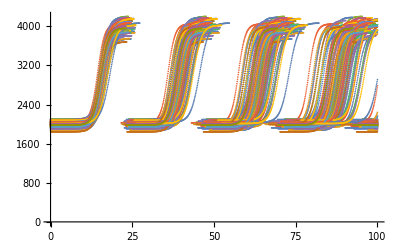

```mathematica
ListPlot[cells[[1;;100]],ImageSize->400]
```

```mathematica
cellsforasf1=Table[cells[[All,i,2]],{i,1,1000}];
```

```mathematica
cellsforasf2=Prepend[Table[cellsforasf1[[i+120]],{i,80,880,80}],cellsforasf1[[1+120]]];
```

```mathematica
ASF=Table[KuiperTest[cellsforasf2[[i]],cellsforasf2[[i+1]],"TestStatistic"],{i,1,11}]
```

{1.,1.,0.479,0.966,0.952,0.464,0.803,0.8,0.437,0.573,0.61}